# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]][[1;;-1]]
```

{D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=30.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=32.5.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=35.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=37.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=40.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=42.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=46.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=47.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=50.2.xlsx}

```mathematica
temps=(ToExpression@StringRiffle[StringSplit[StringSplit[#,"="][[-1]],"."][[1;;-2]],"."])&/@files
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
data=SortBy[Import[#][[1]],First]&/@files;
```

## Processing

```mathematica
cutData=data[[All,-4;;-1,{1,2}]]
```

{{{2.,13.75},{2.5,11.},{3.,9.},{3.5,7.75}},{{2.,14.5},{2.5,11.5},{3.,9.5},{3.5,8.25}},{{2.,14.25},{2.5,11.5},{3.,9.5},{3.5,8.}},{{2.,15.},{2.5,12.},{3.,10.},{3.5,8.5}},{{2.,15.},{2.5,12.},{3.,9.5},{3.5,8.}},{{2.,15.5},{2.5,12.5},{3.,10.25},{3.5,8.75}},{{2.,15.25},{2.5,12.25},{3.,10.},{3.5,8.5}},{{2.,15.5},{2.5,12.5},{3.,10.},{3.5,8.5}},{{2.,15.5},{2.5,12.5},{3.,10.},{3.5,8.5}},{{2.,15.5},{2.5,12.5},{3.,10.25},{3.5,8.75}},{{2.,15.5},{2.5,12.5},{3.,10.25},{3.5,8.75}},{{2.,16.},{2.5,12.5},{3.,10.5},{3.5,8.75}},{{2.,16.},{2.5,13.},{3.,10.5},{3.5,9.}}}

```mathematica
processedData=Map[{1/#[[1]], #[[1]]#[[2]]}&,cutData,{2}];
```

```mathematica
cols=ColorData["ThermometerColors"]/@Rescale[temps];
```

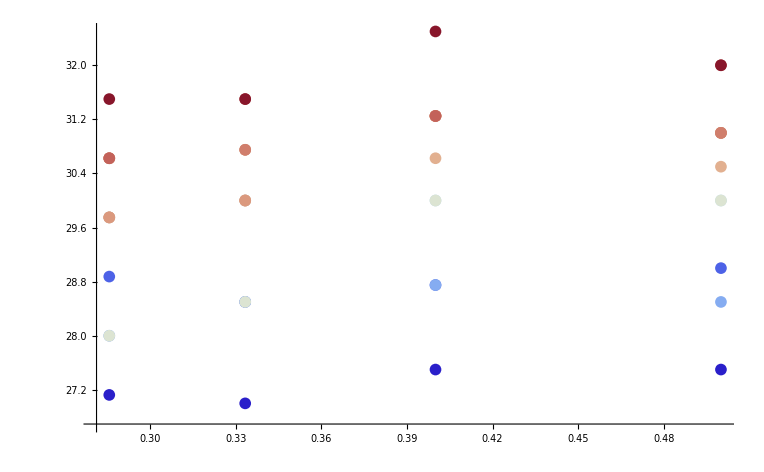

```mathematica
ListPlot[processedData,PlotRange->All,PlotStyle->cols]
```